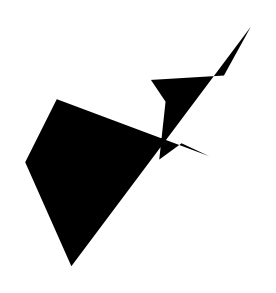
```mathematica
DiscretizeRegion[-Graphics-]
```

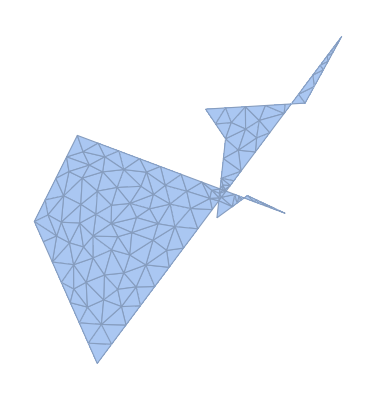

```mathematica
Area[-Graphics-]
```

21.2447

```mathematica
Area[DiscretizeRegion[Region[Polygon[Pin[[Ans[[2]]]]]]]]
```

39.8586

```mathematica
Area[DiscretizeRegion[Region[Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop1]]]]]]]
```

29.0396

```mathematica
Area[DiscretizeRegion[Region[Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop3]]]]]]]
```

17.9052

```mathematica
Pin={{9.25288,8.29378},{2.70712,8.11709},{9.07998,1.31631},{1.93951,5.50628},{7.72967,0.273102},{8.12179,9.14533},{7.65083,7.41157},{1.62292,8.16103},{9.49436,8.82514},{1.10565,8.81871}};(*Point input*)
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
Ans=FindShortestTour[Pin];
PDRank=Ordering[PD];
AbsCurr =Abs[Curr ];
CurrRank=Ordering[1/AbsCurr ];(* 昇順 *)
PDCurrRank=Ordering[PD/AbsCurr];(* 昇順 *)
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]];
PDWeightCurrRank=Ordering[PDWeight/AbsCurr ];
AnsA=Area[DiscretizeRegion[Region[Polygon[Pin[[Ans[[2]]]]]]]];
PDRankA=Area[DiscretizeRegion[Region[Polygon[Pin[[VertexSortFromLoopEdgeList[GreedyRank[PDRank]]]]]]]];
CurrRankA=Area[DiscretizeRegion[Region[Polygon[Pin[[VertexSortFromLoopEdgeList[GreedyRank[CurrRank]]]]]]]];
PDCurrRankA=Area[DiscretizeRegion[Region[Polygon[Pin[[VertexSortFromLoopEdgeList[GreedyRank[PDCurrRank]]]]]]]];
PDWeightCurrRankA=Area[DiscretizeRegion[Region[Polygon[Pin[[VertexSortFromLoopEdgeList[GreedyRank[PDWeightCurrRank]]]]]]]];
AnsA
PDRankA
CurrRankA
PDCurrRankA
PDWeightCurrRankA
```

39.8586

29.0396

43.164

17.9052

17.9052

```mathematica
{{{1,9},{6,7}},{{1,9},{7,4}},{{1,9},{4,2}},{{1,9},{2,8}},{{1,9},{8,10}},{{1,9},{10,5}},{{1,9},{5,3}},{{9,6},{7,4}},{{9,6},{4,2}},{{9,6},{2,8}},{{9,6},{8,10}},{{9,6},{10,5}},{{9,6},{5,3}},{{9,6},{3,1}},{{6,7},{4,2}},{{6,7},{2,8}},{{6,7},{8,10}},{{6,7},{10,5}},{{6,7},{5,3}},{{6,7},{3,1}},{{7,4},{2,8}},{{7,4},{8,10}},{{7,4},{10,5}},{{7,4},{5,3}},{{7,4},{3,1}},{{4,2},{8,10}},{{4,2},{10,5}},{{4,2},{5,3}},{{4,2},{3,1}},{{2,8},{10,5}},{{2,8},{5,3}},{{2,8},{3,1}},{{8,10},{5,3}},{{8,10},{3,1}},{{10,5},{3,1}}}[[{23,27}]]
```

{{{7,4},{10,5}},{{4,2},{10,5}}}

```mathematica
Pin
```

{{2.43518,8.44989},{9.28756,2.77386},{3.07066,3.18809},{4.79991,8.6434},{8.62791,8.03928},{7.18134,7.14019},{4.4599,5.31044},{8.68489,5.42457},{1.97656,1.93274},{4.90035,3.08683}}

```mathematica
Pinx=Pin[[All,1]]
```

{9.25288,2.70712,9.07998,1.93951,7.72967,8.12179,7.65083,1.62292,9.49436,1.10565}

```mathematica
Piny=Pin[[All,2]]
```

{8.29378,8.11709,1.31631,5.50628,0.273102,9.14533,7.41157,8.16103,8.82514,8.81871}

```mathematica
Variance[Pin[[All,1]]]
```

7.41365

```mathematica
Variance[Pin[[All,2]]]
```

6.55399

```mathematica
Max[Pinx]-Min[Pinx]
```

7.311

```mathematica
Min[Pin[[All,1]]]
```

1.97656

```mathematica
Max[Pin[[All,2]]]
```

8.6434

```mathematica
Mean[Pinx]
```

5.87047

```mathematica
Mean[Piny]
```

6.58683

```mathematica
PinCenter={Mean[Pinx],Mean[Piny]}
```

{5.87047,6.58683}

```mathematica
Pin[[1]]
```

{9.25288,8.29378}

```mathematica
EuclideanDistance[PinCenter,Pin[[1]]]
```

3.78871

```mathematica
Length[Pin]
```

10

```mathematica
Table[EuclideanDistance[PinCenter,Pin[[i]]],{i,Length[Pin]}]
```

{3.78871,3.51404,6.17085,4.07677,6.58178,3.40798,1.96211,4.52988,4.25941,5.26163}

```mathematica
Variance[Table[EuclideanDistance[PinCenter,Pin[[i]]],{i,Length[Pin]}]]
```

1.87174